### Wprowadzenie wartości dla temperatury śniegu ( "T" ), masy śniegu padającej w jednostce czasu na jednostkę powierzchni szkła ( "M" ), ciepła właściwego ( "c" ) i topnienia ( "λ" ) śniegu, sprawności urządzenia ( "η" ) i oporu szyby ( "R" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
T=-2 ;                  (* °C *)
```

```mathematica
M=0.1;                 (* kg/(m^2 s) *)
```

```mathematica
c= 2100;               (* J/(kg K) *)
```

```mathematica
λ=3.35×10^5;     (* J/K *)
```

```mathematica
η=0.45;                  (* 1 *)
```

```mathematica
R=Rs×l/W;
```

### Wprowadzenie wzorów na moc wydzielaną w szkle ( "P" ) ( "U" oznacza napięcie przyłożone do szyby) i na moc przypadającą na jednostkę powierzchni okna ( "P_s" ).

```mathematica
P=η×U^2/R;
Ps=P/S;
```

### Wprowadzenie wzorów na przyrost temperatury śniegu ( "ΔT" ) i na ciepło, które trzeba dostarczyć aby go stopić ( "ΔQ" ).

```mathematica
ΔT=0-T;
ΔQ=M×(c×ΔT+λ);
```

### Wykorzystanie bilansu energii do obliczenie napięcia przyłożonego do szyby.

```mathematica
A=Solve[Ps==ΔQ,U]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{U→-(274.55 √l √Rs √S)/(√W)},{U→(274.55 √l √Rs √S)/(√W)}}

### Sporządzenie wykresu obrazującego zależność napięcia przyłożonego do szyby od jej pola powierzchni.

```mathematica
l=1*W;
```

```mathematica
U1=U/.A[[2,1]];
```

```mathematica
rys1=Plot[U1/.Rs->0.5×10^-3,{S,0.5,1},
PlotStyle->{Black,Thickness[0.006]}];
```

```mathematica
rys2=Plot[U1/.Rs->1×10^-3,{S,0.5,1},
PlotStyle->{Gray,Thickness[0.006]}];
```

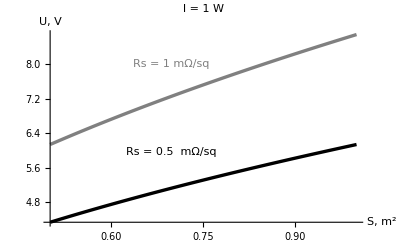

```mathematica
Show[rys1,rys2,PlotRange->All,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[" l = 1 W",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"S, m^2","U, V "},
Prolog->{Text[StyleForm["Rs = 0.5  mΩ/sq",FontColor->Black],
Scaled[{0.40,0.38}]],
Text[StyleForm["Rs = 1 mΩ/sq",FontColor->Gray],
Scaled[{0.40,0.83}]]}]
```

```mathematica
l=0.5*W;
```

```mathematica
U2=U/.A[[2,1]];
```

```mathematica
rys3=Plot[U2/.Rs->0.5×10^-3,{S,0.5,1},
PlotStyle->{Black,Thickness[0.006]}];
```

```mathematica
rys4=Plot[U2/.Rs->1×10^-3,{S,0.5,1},
PlotStyle->{Gray,Thickness[0.006]}];
```

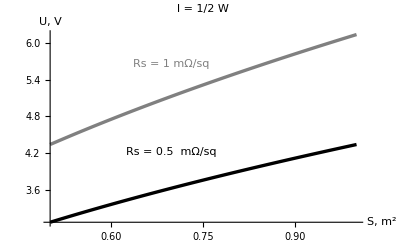

```mathematica
Show[rys3,rys4,PlotRange->All,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[" l = 1/2 W",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"S, m^2","U, V "},
Prolog->{Text[StyleForm["Rs = 0.5  mΩ/sq",FontColor->Black],
Scaled[{0.40,0.38}]],
Text[StyleForm["Rs = 1 mΩ/sq",FontColor->Gray],
Scaled[{0.40,0.83}]]}]
```